```mathematica
Res[h_,a_,L_]=1/Simplify[Integrate[1/(h+a(L/2)^2-a(l-L/2)^2)/L,{l,0,L}],{h>0,a>0,L>0}]
```

(L √(a (4 h+a L^2)))/(4 ArcTanh[L √(a/(4 h+a L^2))])

```mathematica
Rform[h_,a_,L_,l_]:=(h+a(L/2)^2-a(l-L/2)^2);
```

```mathematica
Res[3,.00001,4]
Res[3,.25,4]
Res[3,.5,4]
```

3.00003

3.64096

4.24183

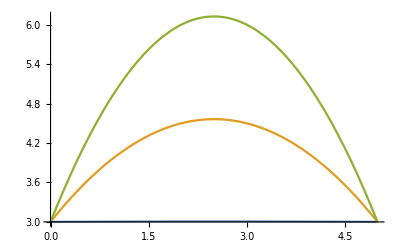

```mathematica
Plot[{Rform[3,0.001,5,l],Rform[3,0.25,5,l],Rform[3,0.5,5,l]},{l,0,5}]
```